Example 2 on p 113

```mathematica
Clear["Global`*"]
```

```mathematica
hank={y'''[x]-y''[x]+100 y'[x]-100 y[x]==0,y[0]==4,y'[0]==11,y''[0]==-299}
dank=DSolve[hank,y[x],x]
```

{-100 y[x]+100 y'[x]-y''[x]+y^(3)[x]==0,y[0]==4,y'[0]==11,y''[0]==-299}

{{y[x]→ⅇ^x+3 Cos[10 x]+Sin[10 x]}}

Above: This answer agrees with the text.

1 - 6 General solution
Solve the given ODE.

1.  y''' + 25 y' = 0

```mathematica
Clear["Global`*"]
```

```mathematica
jav=y'''[x]+25 y'[x]==0
nav=DSolve[jav,y[x],x]
```

25 y'[x]+y^(3)[x]==0

{{y[x]→C[3]-1/5 C[2] Cos[5 x]+1/5 C[1] Sin[5 x]}}

1. Above: This answer agrees with the text.

3.  y^iv+4y''=0

```mathematica
Clear["Global`*"]
```

```mathematica
har=y''''[x]+4 y''[x]==0
mar=DSolve[har,y[x],x]
```

4 y''[x]+y^(4)[x]==0

{{y[x]→C[3]+x C[4]-1/4 C[1] Cos[2 x]-1/4 C[2] Sin[2 x]}}

1. Above: This answer agrees with the text.

5.  (D^4+10 D^2+9I)y=0

```mathematica
Clear["Global`*"]
```

```mathematica
yip=y''''[x]+10 y''[x]+9 y[x]==0
nip=DSolve[yip,y[x],x]
```

9 y[x]+10 y''[x]+y^(4)[x]==0

{{y[x]→C[3] Cos[x]+C[1] Cos[3 x]+C[4] Sin[x]+C[2] Sin[3 x]}}

1. Above: This answer agrees with the text.

7 - 13 Initial value problem
Solve the IVP by a CAS, giving a general solution and the particular solution and its graph.

7.  y''' + 3.2 y'' + 4.81 y' = 0, y[0] = 3.4, y'[0] = -4.6, y''[0] = 9.91

```mathematica
Clear["Global`*"]
```

```mathematica
de=y'''[x]+3.2 y''[x]+ 4.81 y'[x]==0
gs=DSolve[de,y[x],x]
```

4.81 y'[x]+3.2 y''[x]+y^(3)[x]==0

{{y[x]→C[3]+ⅇ^(-1.6 x) ((-0.31185 C[1]-0.33264 C[2]) Cos[1.5 x]+(-0.33264 C[1]+0.31185 C[2]) Sin[1.5 x])}}

```mathematica
gsf=gs/.{C[1]->1,C[2]->1,C[3]->1}
```

{{y[x]→1+ⅇ^(-1.6 x) (-0.644491 Cos[1.5 x]-0.02079 Sin[1.5 x])}}

```mathematica
de2={y'''[x]+3.2 y''[x]+ 4.81 y'[x]==0,y[0]==3.4,y'[0]==-4.6,y''[0]==9.91}
```

{4.81 y'[x]+3.2 y''[x]+y^(3)[x]==0,y[0]==3.4,y'[0]==-4.6,y''[0]==9.91}

```mathematica
ps=DSolve[de2,y[x],x]
```

{{y[x]→2.4 ⅇ^(-1.6 x) (1. ⅇ^(1.6 x)+0.416667 Cos[1.5 x]-0.833333 Sin[1.5 x])}}

```mathematica
trim=Expand[ps]
```

{{y[x]→2.4+1. ⅇ^(-1.6 x) Cos[1.5 x]-2. ⅇ^(-1.6 x) Sin[1.5 x]}}

1. Above: The answer agrees with that of the text to 2S.

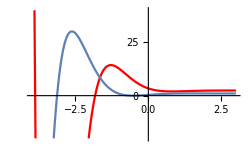

```mathematica
plot1=Plot[y[x]/.ps,{x,-4,3},PlotRange->{-20,40},PlotStyle->Red,ImageSize->250];
plot2=Plot[y[x]/.gsf,{x,-4,3},PlotRange->{-20,40}];
Show[plot1,plot2]
```

2. Above: There was an odd gap at the max of gsf the first time it was plotted. Then the constant value of C[1] was jiggled and afterwards the gap disappeared.

9.  4 y''' + 8 y'' + 41 y' + 37 y = 0, y[0] = 9, y'[0] = -6.5, y''[0] = -39.75

```mathematica
Clear["Global`*"]
```

```mathematica
gie=4 y'''[x]+ 8 y''[x]+ 41 y'[x]+37 y[x]==0
gs=DSolve[gie,y[x],x]
```

37 y[x]+41 y'[x]+8 y''[x]+4 y^(3)[x]==0

{{y[x]→ⅇ^-x C[3]+ⅇ^(-x/2) C[2] Cos[3 x]+ⅇ^(-x/2) C[1] Sin[3 x]}}

```mathematica
gse=gs/.{C[1]->1,C[2]->1,C[3]->1}
```

{{y[x]→ⅇ^-x+ⅇ^(-x/2) Cos[3 x]+ⅇ^(-x/2) Sin[3 x]}}

```mathematica
pie={4 y'''[x]+ 8 y''[x]+ 41 y'[x]+37 y[x]==0,y[0]==9,y'[0]==-6.5,y''[0]==-39.75}
ps=DSolve[pie,y[x],x]
```

{37 y[x]+41 y'[x]+8 y''[x]+4 y^(3)[x]==0,y[0]==9,y'[0]==-6.5,y''[0]==-39.75}

{{y[x]→5. ⅇ^-x (0.8+1. ⅇ^(x/2) Cos[3 x]+6.09497×10^-18 ⅇ^(x/2) Sin[3 x])}}

```mathematica
pse=Expand[ps]
```

{{y[x]→4. ⅇ^-x+5. ⅇ^(-x/2) Cos[3 x]+3.04749×10^-17 ⅇ^(-x/2) Sin[3 x]}}

```mathematica
Chop[pse,10^-16]
```

{{y[x]→4. ⅇ^-x+5. ⅇ^(-x/2) Cos[3 x]}}

1. Above: The answer agrees with the text’s.

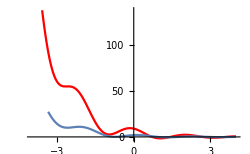

```mathematica
plot1=Plot[y[x]/.pse,{x,-4,4},PlotRange->Automatic,PlotStyle->Red,ImageSize->250];
plot2=Plot[y[x]/.gse,{x,-4,4},PlotRange->Automatic];
Show[plot1,plot2]
```

11.  y^iv-9y''-400y=0, y[0]=0, y'[0]=0, y''[0]=41, y'''[0]=0

```mathematica
Clear["Global`*"]
```

```mathematica
nom=y''''[x]-9 y''[x]-400 y[x]==0
gs=DSolve[nom,y[x],x]
```

-400 y[x]-9 y''[x]+y^(4)[x]==0

{{y[x]→ⅇ^(-5 x) C[3]+ⅇ^(5 x) C[4]+C[1] Cos[4 x]+C[2] Sin[4 x]}}

```mathematica
gse=gs/.{C[1]->1,C[2]->1,C[3]->1,C[4]->1}
```

{{y[x]→ⅇ^(-5 x)+ⅇ^(5 x)+Cos[4 x]+Sin[4 x]}}

```mathematica
nomp={y''''[x]-9 y''[x]-400 y[x]==0,y[0]==0,y'[0]==0,y''[0]==41,y'''[0]==0}
ps=DSolve[nomp,y[x],x]
```

{-400 y[x]-9 y''[x]+y^(4)[x]==0,y[0]==0,y'[0]==0,y''[0]==41,y^(3)[0]==0}

{{y[x]→1/2 ⅇ^(-5 x) (1+ⅇ^(10 x)-2 ⅇ^(5 x) Cos[4 x])}}

```mathematica
ps1=ExpToTrig[ps]
```

{{y[x]→1/2 (Cosh[5 x]-Sinh[5 x]) (1-2 Cos[4 x] Cosh[5 x]+Cosh[10 x]-2 Cos[4 x] Sinh[5 x]+Sinh[10 x])}}

```mathematica
ps2=Expand[ps1]
```

{{y[x]→1/2 Cosh[5 x]-Cos[4 x] Cosh[5 x]^2+1/2 Cosh[5 x] Cosh[10 x]-1/2 Sinh[5 x]-1/2 Cosh[10 x] Sinh[5 x]+Cos[4 x] Sinh[5 x]^2+1/2 Cosh[5 x] Sinh[10 x]-1/2 Sinh[5 x] Sinh[10 x]}}

```mathematica
ps3=Simplify[ps2]
```

{{y[x]→-Cos[4 x]+Cosh[5 x]}}

1. Above: The answer matches the text’s.

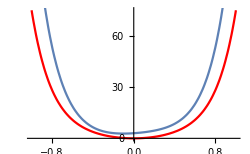

```mathematica
plot1=Plot[y[x]/.ps3,{x,-1,1},PlotRange->Automatic,PlotStyle->Red,ImageSize->250];
plot2=Plot[y[x]/.gse,{x,-1,1},PlotRange->Automatic];
Show[plot1,plot2]
```

13.  y^iv+0.45y'''-0.165y''+0.0045y'-0.00175y=0, y[0]=17.4, y'[0]=-2.82, y''[0]=2.0485, y'''[0]=-1.458675

```mathematica
Clear["Global`*"]
```

```mathematica
bi=y''''[x]+0.45 y'''[x]-0.165 y''[x]+0.0045 y'[x]-0.00175 y[x]==0
gs=DSolve[bi,y[x],x]
```

-0.00175 y[x]+0.0045 y'[x]-0.165 y''[x]+0.45 y^(3)[x]+y^(4)[x]==0

{{y[x]→ⅇ^(-0.7 x) C[1]+ⅇ^(0.25 x) C[4]+1. C[3] Cos[0.1 x]+1. C[2] Sin[0.1 x]}}

```mathematica
gse=gs/.{C[1]->1,C[2]->1,C[3]->1,C[4]->1}
```

{{y[x]→ⅇ^(-0.7 x)+ⅇ^(0.25 x)+1. Cos[0.1 x]+1. Sin[0.1 x]}}

```mathematica
bip={y''''[x]+0.45 y'''[x]-0.165 y''[x]+0.0045 y'[x]-0.00175 y[x]==0,y[0]==17.4,y'[0]==-2.82,y''[0]==2.0485,y'''[0]==-1.458675}
ps=DSolve[bip,y[x],x]
```

{-0.00175 y[x]+0.0045 y'[x]-0.165 y''[x]+0.45 y^(3)[x]+y^(4)[x]==0,y[0]==17.4,y'[0]==-2.82,y''[0]==2.0485,y^(3)[0]==-1.45868}

{{y[x]→1. ⅇ^(-0.7 x) (4.3+1. ⅇ^(0.95 x)+12.1 ⅇ^(0.7 x) Cos[0.1 x]-0.6 ⅇ^(0.7 x) Sin[0.1 x])}}

```mathematica
droop=Expand[ps]
```

{{y[x]→4.3 ⅇ^(-0.7 x)+1. ⅇ^(0.25 x)+12.1 Cos[0.1 x]-0.6 Sin[0.1 x]}}

1. Above: The answer matches the text’s.

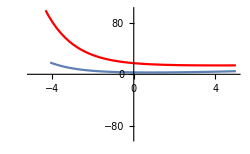

```mathematica
plot1=Plot[y[x]/.droop,{x,-5,5},PlotRange->{-100,100},PlotStyle->Red,ImageSize->250];
plot2=Plot[y[x]/.gse,{x,-5,5},PlotRange->Automatic];
Show[plot1,plot2]
```